```mathematica
ClearAll["Global`*"]
```

```mathematica
P0=0.0477;
μ=0.32;
σ=0.26;
c=0.89;
n=Ceiling[t-x];
xr=1;
A=2.6;
β0=1.35;
β[t_]=β0*A*t^(A-1)/xr^A;
```

```mathematica
P[t_,x_]=Piecewise[{
	{P0*PDF[NormalDistribution[μ,σ],x-t]*ⅇ^(-c*x),x≥t && x-t≤0},
	{P0*PDF[NormalDistribution[μ,σ],x-t]*ⅇ^(-c*t),x≥t && x-t>0},
	{β[t]^n*P0*PDF[NormalDistribution[μ,σ],x-t]*ⅇ^(-n*c)*ⅇ^(-c*x),x<t && t-x≥ 1},
	{β[t]^n*P0*PDF[NormalDistribution[μ,σ],x-t]*ⅇ^(-c*t),x<t && t-x<1}
},0];
```

```mathematica
Block[{Internal`Integrate`debugSwitch=10},Tot[t_]=Integrate[P[t,x],{x,0,1}]]
```

$Aborted

```mathematica
Ring[t_]=Integrate[P[t,x],{x,0,0.5}];
Late[t_]=Tot[t]-Ring[t];
```

$Aborted

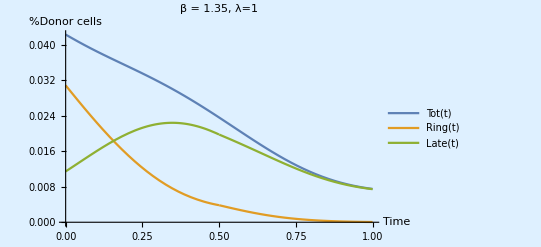

```mathematica
Plot[{Tot[t],Ring[t],Late[t]},{t,0,1}, PlotLabel-> "β = 1.35, λ=1",PlotLegends->"Expressions",Background->LightBlue, AxesLabel-> {"Time","%Donor cells"}]
```

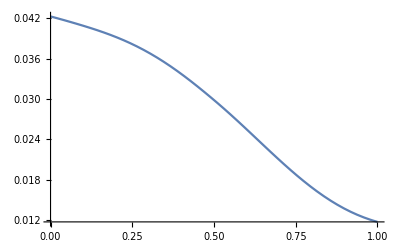

```mathematica
Plot[{Tot[t]},{t,0,1}]
```

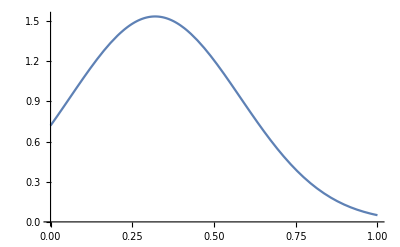

```mathematica
Plot[{PDF[NormalDistribution[μ,σ],x]},{x,0,1}]
```

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x],{x,0,0.5}]
```

0.646423

```mathematica
Late[1]
```

0.0108731

```mathematica
ClearAll["Global`*"]
```

```mathematica
P0=0.0477;
μ=0.32;
σ=0.26;
c=0.89;
n=Ceiling[t-x];
xr=1.;
A=2.6;
β=0.4;
xc=0.5;
λ=1;
(*β[t_]=β0*A*t^(A-1)/xr^A;*)
```

```mathematica
P2[t_,x_]=Piecewise[{
	{P0*PDF[NormalDistribution[μ,σ],x-t*λ],x≥t*λ &&x<xc},
	{P0*PDF[NormalDistribution[μ,σ],x-t*λ]*ⅇ^(-c/λ*(x-xc)),x≥t*λ &&x≥xc&& x-t*λ≤xc},
	{P0*PDF[NormalDistribution[μ,σ],x-t*λ]*ⅇ^(-c*t*λ),x≥t*λ && x≥ xc&& x-t*λ>xc},
	{β^n*P0*PDF[NormalDistribution[μ,σ],n+x-t*λ]*ⅇ^(-(n*c)/λ*(1-xc)),x<t*λ &&x<xc&& t*λ-x≥ 1-xc},
	{β^n*P0*PDF[NormalDistribution[μ,σ],n+x-t*λ]*ⅇ^(-c/λ*(t*λ-x-(n-1)*xc)),x<t*λ && x<xc&& t*λ-x< 1-xc},
	{β^n*P0*PDF[NormalDistribution[μ,σ],n+x-t*λ]*ⅇ^(-(n*c)/λ*(1-xc))*ⅇ^(-c/λ*(x-xc)),x<t*λ &&x≥xc&& t*λ-x≥ 1-xc},
	{β^n*P0*PDF[NormalDistribution[μ,σ],n+x-t*λ]*ⅇ^(-c/λ*(t*λ-n*xc)),x<t*λ &&x≥xc&& t*λ-x<1-xc}
},0];
```

```mathematica
Tot[t_]=Integrate[P2[t,x],{x,0,1.}];
```

```mathematica
Ring[t_]=Integrate[P2[t,x],{x,0,0.5}];
```

$Aborted

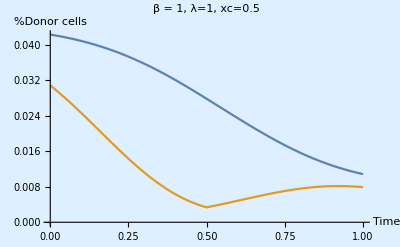

```mathematica
Plot[{Integrate[P2[t,x],{x,0,1.}],Integrate[P2[t,x],{x,0,0.5}]},{t,0,1.}, PlotLabel-> "β=0.44, λ=1, xc=0.5",Background->LightBlue, AxesLabel-> {"Time","%Donor cells"}]
```